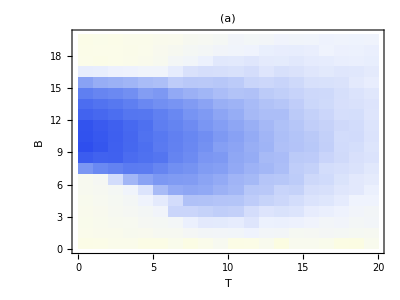

```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["heat1.csv","Data"];
a=Transpose[a];
b=Mean[a];
Dimensions[b];
b=ArrayReshape[b,{20,20}];
b=Reverse[b,2];
MatrixPlot[b,FrameTicks->ftick,ColorFunction->"TemperatureMap",DataReversed->True, AspectRatio->0.75,PlotLabel->Style["(a)",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[B,FontSize->16],Style[T,FontSize->16]}]
```

```mathematica
Dimensions[b]
```

{20,20}

```mathematica
b[[1,1]]
```

0.5831770228457732

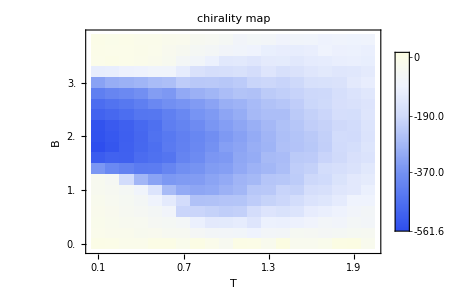

```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["heat1.csv","Data"];
a=Transpose[a];
b=Mean[a];
Dimensions[b];
b=ArrayReshape[b,{20,20}];
b=Reverse[b,2];
Ttick=Table[{i,(i)/10.0},{i,1,30,3}];
Btick=Table[{i,(i-1)/5.0},{i,1,30,5}];
MatrixPlot[b,FrameTicks->{Btick,Ttick},FrameTicksStyle->Directive[Black,12],ColorFunction->"TemperatureMap",DataReversed->True, AspectRatio->0.75,PlotLabel->Style["chirality map",FontSize->20],PlotLegends->{Automatic},FrameLabel->{Style[B,FontSize->16],Style[T,FontSize->16]}]
```